# Introduction to SPQR

SPQR is a package for performing multivariate polynomial and rational function division, as well as related functionality. In this tutorial we outline the core functionality of the package, as well as showcase various examples and applications.

For functionality covered beyond this tutorial, detailed documentation for every function can be accessed via the guide page SPQR or the individual function documentation pages, eg SPQRDet.

Loading the Package

```mathematica
Get["SPQR`"]
```

## Polynomial and Rational Function Division

In this section, we describe how companion matrices can be used to perform polynomial and rational function division in SPQR. Before diving into an example, it is useful to see a high level overview of SPQR's "pipeline" for such computations

```mathematica
-Graphics-;
```

SPQR takes as input a polynomial ideal (system of equations), as well as a list of target functions to reduce. First, this information is used to find a set of irreducible monomials with FindIrreducibleMonomials. This information is then passed to BuildCompanionMatrices, which builds a set of companion matrices M_x for each variable in the ideal. Next, BuildTargetCompanionMatrices constructs a list of companion matrices for the functions f, M_f. Finally, the result of polynomial division is reconstructed with ReconstructTargetCompanionMatrices.

We delegate further mathematical discussion to manuscript accompanying this package, and here focus on the computational commands.

### A first example

We showcase the pipeline described above with an example

We begin by defining an ideal in two variables {x,y}, and one parameter {a}

```mathematica
variables = {x,y};
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

as well as three target functions to reduce. The first two are polynomials, whilst the last is a rational function

```mathematica
f ={a*x^5*y^5*y^2+3+x*y^2,x*y^2,(a+x+1/y)/((x/(y-3)+y^2)^2)};
```

The irreducible monomials for this ideal are found by probing the Groebner basis for this ideal numerically once:

```mathematica
irreds=FindIrreducibleMonomials[ideal,variables]
```

{y^5,y^4,y^3,y^2,y,1}

We can then generate the companion matrices using BuildCompanionMatrices. A companion matrix is generated for each variable (not parameter) in the system, so in this case {x,y}

```mathematica
weight = {1,10};
cmats = BuildCompanionMatrices[ideal,variables,weight,irreds];
```

system closed at weight: 4

The 3rd input to BuildCompanionMatrices specifies a minimum and maximum weight to which SPQR should generate the Macaulay system of equations required for building companion matrices.

SPQR begins at the lowest weight, and increments it until resulting system is large enough. This is done by comparing the results of internal checks against the provided irreducible monomials. The command terminates either when the weight is large enough or the maximum input has been reached. For example, if we make the maximum weight too small,

```mathematica
tooSmallWeight = {1,3};
BuildCompanionMatrices[ideal,variables,tooSmallWeight,irreds]
```

Irreducible monomials do not match. Try increasing the system size

Found 8 monomials: {x y^5,y^6,y^5,y^4,y^3,y^2,y,1}

$Failed

The output cmats itself simply contains data for its corresponding SPQR graph that is required for other functions to work correctly. The first output is the name of the FiniteFlow graph. The second output is the list of parameters of the ideal. The third output is the list of irreducible monomials, in vector notation. The fourth output is the name of the companion matrices generated in the FiniteFlow graph. Finally the fifth output is simply the set of variables in the ideal.

```mathematica
cmats
```

{SPQRGraph$477760,{a,extraparam},{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},{SPQR`Private`m[x$139],SPQR`Private`m[y$140]},{x,y}}

A schematic of the FiniteFlow graph can be seen with the following command, where the two outputs correspond to the two companion matrices M_x and M_y.

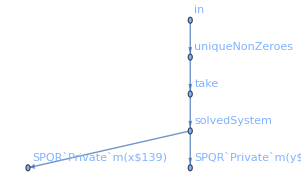

```mathematica
cmats // First // FFGraphDraw
```

The next step in the procedure is to produce a companion matrix for the polynomial we want to reduce. This can be achieved with BuildTargetCompanionMatrices. The parsing and building of the rational functions is automatically handled and can accept rational expressions to arbitrary depth

```mathematica
fcmats = BuildTargetCompanionMatrices[f,cmats]
```

{SPQRGraph$477760,{a,extraparam},{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},{SPQR`Private`m[o$141],SPQR`Private`m[o$142],SPQR`Private`m[o$143]},{x,y}}

This command will parse the expression given in Mathematica and will automatically construct the relevant graph in FiniteFlow

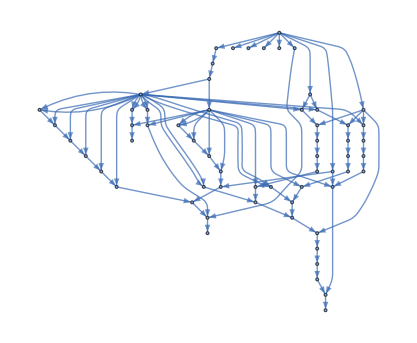

```mathematica
fcmats // First // FFGraphDraw // FullForm // ReplaceAll[Text[___]:>Text[""]] // Normal // First
```

Finally, we can extract the output of the polynomial division from the target companion matrix, with the command ReconstructTargetCompanionMatrices

```mathematica
result = ReconstructTargetCompanionMatrices[fcmats];
result[[1;;2]]
result[[3;;3]]//Short
```

Generated 20 sample points

Approximate time per evaluation (single core): 2.1e-05 sec.

Generated 20 sample points

Approximate time per evaluation (single core): 1.7e-05 sec.

{(1/2+(9 a)/2+3 a^2+(49 a^3)/16)/a^3+((-3-(117 a)/4-(171 a^2)/8-(7 a^3)/16) y)/a^3+((5/2+36 a+36 a^2+(41 a^3)/16) y^2)/a^3+((-3-(153 a)/4-(315 a^2)/8-(97 a^3)/16) y^3)/a^3+((1/2+(33 a)/2+(27 a^2)/2+(55 a^3)/16) y^4)/a^3+((-9/4-(9 a)/8-(9 a^2)/16) y^5)/a^2,y/2-(3 y^2)/2+y^3/2}

{(4364745/96721+«9»)/(1+(3211 a)/1555+«5»+(451 a^7)/309507200+a^8/619014400)+((«1») y)/(1+«7»+(«1»)/(«9»))+«1»+«1»+(«1»)/(«1»)+((«1») y^5)/(1+«7»+a^8/(61«4»400))}

We can check the first two polynomials divide correctly with

```mathematica
gb = GroebnerBasis[ideal,variables,CoefficientDomain->RationalFunctions];
gbAns=PolynomialReduce[f[[1;;2]],gb,variables]//Map[Last]
result[[1;;2]] - gbAns // Factor // ContainsOnly[#,{0}]&
```

{(8+72 a+48 a^2+49 a^3)/(16 a^3)+((-48-468 a-342 a^2-7 a^3) y)/(16 a^3)+((40+576 a+576 a^2+41 a^3) y^2)/(16 a^3)+((-48-612 a-630 a^2-97 a^3) y^3)/(16 a^3)+((8+264 a+216 a^2+55 a^3) y^4)/(16 a^3)-(9 (4+2 a+a^2) y^5)/(16 a^2),y/2-(3 y^2)/2+y^3/2}

True

Mathematica does not support multivariate polynomial division of rational functions. However, it is at least possible to check that the result is correct with the following code

```mathematica
PolynomialReduce[result[[3]]*(f[[3]]//Together//Denominator),gb,variables][[2]]//Factor;
PolynomialReduce[(f[[3]]//Together//Numerator),gb,variables][[2]]//Factor;
%==%%//Factor
```

True

We note that SPQR did not require the explicit generation of a Groebner basis to obtain the correct reductions.

### Monomial Orders

By default, Lexicographic order is used for computing divisions. This can be changed by passing the option "MonomialOrder" to BuildCompanionMatrices. Make sure to also pass the same option to FindIrreducibleMonomials! Concretely, we can use the same example as above

The same steps are run through but with DegreeReverseLexicographic ordering. We note that this ordering required a lower weight for the Macaulay system to close. This reflects the general understanding that this ordering is considered "easier" than Lexicographic

```mathematica
irreds=FindIrreducibleMonomials[ideal,variables,"MonomialOrder"->DegreeReverseLexicographic]
cmats = BuildCompanionMatrices[ideal,variables,weight,irreds,"MonomialOrder"->DegreeReverseLexicographic];
```

{y^3,x^2,y^2,x,y,1}

system closed at weight: 3

The rest proceeds as before

```mathematica
fcmats = BuildTargetCompanionMatrices[f,cmats];
result = ReconstructTargetCompanionMatrices[fcmats,"DeleteGraph"->False];
result[[1;;2]]
result[[3;;3]]//Short
```

Generated 20 sample points

Approximate time per evaluation (single core): 2e-05 sec.

{(-6-(45 a)/2-(291 a^2)/4-(9 a^3)/8+3 a^4)/a^4+((-9-(9 a)/2-(9 a^2)/4) x)/a^3+((4+24 a+54 a^2+a^3/2) x^2)/a^4+((-18-18 a+(63 a^2)/4+a^3/2) y)/a^3+((24+3 a-(153 a^2)/4-(3 a^3)/2) y^2)/a^3+((-9/2+(9 a)/4+(99 a^2)/8+a^3/2) y^3)/a^3,y/2-(3 y^2)/2+y^3/2}

{(1146711/96721+«8»+(677 a^9)/619014400)/(1+(3211 a)/1555+«5»+(451 a^7)/309507200+a^8/619014400)+(«1»)/(«1»)+«1»+«1»+(«1»)/(«1»)+((«1») y^3)/(1+«7»+(«1»)/(«8»0))}

Checks against Mathematica

```mathematica
gb = GroebnerBasis[ideal,variables,CoefficientDomain->RationalFunctions,MonomialOrder->DegreeReverseLexicographic];
gbAns=PolynomialReduce[f[[1;;2]],gb,variables,MonomialOrder->DegreeReverseLexicographic]//Map[Last]
result[[1;;2]] - gbAns // Factor // ContainsOnly[#,{0}]&
```

{(3 (-16-60 a-194 a^2-3 a^3+8 a^4))/(8 a^4)-(9 (4+2 a+a^2) x)/(4 a^3)+((8+48 a+108 a^2+a^3) x^2)/(2 a^4)+((-72-72 a+63 a^2+2 a^3) y)/(4 a^3)-(3 (-32-4 a+51 a^2+2 a^3) y^2)/(4 a^3)+((-36+18 a+99 a^2+4 a^3) y^3)/(8 a^3),y/2-(3 y^2)/2+y^3/2}

True

```mathematica
PolynomialReduce[result[[3]]*(f[[3]]//Together//Denominator),gb,variables,MonomialOrder->DegreeReverseLexicographic][[2]]//Factor;
PolynomialReduce[(f[[3]]//Together//Numerator),gb,variables,MonomialOrder->DegreeReverseLexicographic][[2]]//Factor;
%==%%//Factor
```

True

## Elimination Theory

SPQR provides functionality for eliminating variables from polynomial ideals. The package provides three distinct ways to do this: via companion matrices and characteristic polynomials, via fitting companion matrices, and via elimination monomial orderings. The first two approaches have the advantage that the companion matrices can be built with any monomial ordering.

### Elimination with Characteristic Polynomials of Companion Matrices

To eliminate variables using characteristic polynomials in SPQR, the following pipeline is used

```mathematica
-Graphics-;
```

Similarly to above, companion matrices are built for all variables in the ideal. A (sub)set of these are then sent to BuildCharacteristicPolynomials and ReconstructCharacteristicPolynomials to reconstruct the final result.

We set up a polynomial system

```mathematica
variables = {x,y,z};
ideal = {b+x^2-y+z^2*y+a,a+x^2*z+y*z+c*z^2,a+z+x*y^2+x*y^3z+3+c}; 
ideal // MatrixForm
```

(a+b+x^2-y+y z^2
a+x^2 z+y z+c z^2
3+a+c+x y^2+z+x y^3 z)

Suppose we want to eliminate {x,y} from this system. With Mathematica we can use GroebnerBasis or Eliminate. This may take a few minutes to run

```mathematica
elim=GroebnerBasis[ideal,{z},{x,y},CoefficientDomain->RationalFunctions]//First//Factor; // AbsoluteTiming
elim // Short
```

{33.0336,Null}

-4 a^5+4 a^6-a^7+12 a^5 z-16 a^6 z+5 a^7 z+12 a^4 b z-16 a^5 b z+«837»+6 c z^19+2 a c z^19+c^2 z^19+6 z^20+2 a z^20+2 c z^20+z^21

It can be shown that elim is related to the characteristic polynomial of the companion matrix M_z. To this end, SPQR provides functionality for computing characteristic polynomials with finite fields.

For elimination via characteristic polynomials, the order of the variables does not matter. We thus first begin by (optionally) sorting the variables using SortVariables.  This command will try find an ordering which results in a simpler Macaulay matrix

```mathematica
variablesSorted = SortVariables[ideal,variables,"MonomialOrder"->DegreeReverseLexicographic]
```

{x,z,y}

We proceed by building the companion matrices for the system. The characteristic polynomial is unique no matter the monomial ordering, so we suggest DegreeReverseLexicographic

```mathematica
irreds = FindIrreducibleMonomials[ideal,variablesSorted,"MonomialOrder"->DegreeReverseLexicographic];
cmats = BuildCompanionMatrices[ideal,variablesSorted,{1,10},irreds,"MonomialOrder"->DegreeReverseLexicographic]
```

system closed at weight: 6

{SPQRGraph$480309,{a,b,c},{j[1,0,3],j[0,1,3],j[0,0,4],j[3,0,0],j[1,2,0],j[0,3,0],j[2,0,1],j[1,1,1],j[1,0,2],j[0,1,2],j[0,0,3],j[2,0,0],j[1,1,0],j[0,2,0],j[1,0,1],j[0,1,1],j[0,0,2],j[1,0,0],j[0,1,0],j[0,0,1],j[0,0,0]},{SPQR`Private`m[x$149],SPQR`Private`m[z$150],SPQR`Private`m[y$151]},{x,z,y}}

We then build the characteristic polynomial for z, with the command BuildCharacteristicPolynomials. The second option instructs the function to only build the characteristic polynomial for z (the 2nd variable after sorting)

```mathematica
charp = BuildCharacteristicPolynomials[cmats,{2}]
```

{SPQRGraph$480309,{a,b,c},{j[1,0,3],j[0,1,3],j[0,0,4],j[3,0,0],j[1,2,0],j[0,3,0],j[2,0,1],j[1,1,1],j[1,0,2],j[0,1,2],j[0,0,3],j[2,0,0],j[1,1,0],j[0,2,0],j[1,0,1],j[0,1,1],j[0,0,2],j[1,0,0],j[0,1,0],j[0,0,1],j[0,0,0]},{SPQR`Private`char[z$150]}}

BuildCharacteristicPolynomials implements the Faddeev–LeVerrier algorithm to build each coefficient sequentially. This can be seen by viewing the newly appended FiniteFlow graph

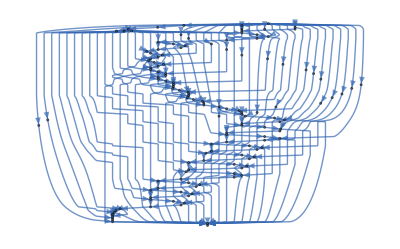

```mathematica
charp // First // FFGraphDraw // FullForm // ReplaceAll[Text[___]:>Text[""]] // Normal // First
```

Finally the result can be reconstructed with the ReconstructCharacteristicPolynomials

```mathematica
rec = ReconstructCharacteristicPolynomials[charp]//First; // AbsoluteTiming
```

Generated 122 sample points

Approximate time per evaluation (single core): 0.000602 sec.

{0.013681,Null}

The characteristic polynomial can then be built by dotting each element of the output list with its respective power of z

```mathematica
elimRec=irreds//Length//Range[0,#]&//Power[z,#]&//Dot[#,rec]&//Factor//Numerator; // AbsoluteTiming
```

{0.006565,Null}

Check against Mathematica

```mathematica
elimRec/elim//Factor
```

-1

### Elimination via Companion Matrix Ansatz

SPQR also supports another method for eliminating variables with companion matrices, by fitting an ansatz. This approach has the advantage that fewer than all variables except one can be eliminated, unlike the characteristic polynomial above. The pipeline for this approach is as follows

```mathematica
-Graphics-;
```

Suppose this time want to only eliminate {x} from the system given above. As before with Mathematica we can use (this may take a few minutes to run):

```mathematica
elim2=GroebnerBasis[ideal,{y,z},{x},CoefficientDomain->RationalFunctions]; // AbsoluteTiming
elim2 // Short[#,5]&
```

{30.781,Null}

{-4 a^5+4 a^6-a^7+(12 a^5-16 a^6+5 a^7+12 a^4 b-16 a^5 b+5 a^6 b) z+(14 a^6-8 a^7-16 a^4 b+40 a^5 b-18 a^6 b-8 a^3 b^2+20 a^4 b^2-9 a^5 b^2-20 a^4 c+24 a^5 c-7 a^6 c) z^2+(-36 a^5+28 a^6-a^7-52 a^4 b+28 a^5 b+9 a^6 b-24 a^3 b^2+15 a^5 b^2-8 a^2 b^3+5 a^4 b^3+48 a^4 c-80 a^5 c+30 a^6 c+48 a^3 b c-80 a^4 b c+30 a^5 b c) z^3+«12»+(504+168 a+168 c+c^5+2 c^6+c^7) z^16+(-42-84 a-14 a^2-84 c-28 a c-14 c^2) z^17+(-84-28 a-28 c) z^18+(-5+6 a+a^2+6 c+2 a c+c^2) z^19+(6+2 a+2 c) z^20+z^21,«525»+(«1») z^20}

With SPQR as before we begin by building companion matrices

With SPQR we as before build companion matrices

```mathematica
variablesSorted = SortVariables[ideal,variables,"MonomialOrder"->DegreeReverseLexicographic]
irreds = FindIrreducibleMonomials[ideal,variablesSorted,"MonomialOrder"->DegreeReverseLexicographic];
cmats = BuildCompanionMatrices[ideal,variablesSorted,{1,10},irreds,"MonomialOrder"->DegreeReverseLexicographic]
```

{x,z,y}

system closed at weight: 6

{SPQRGraph$482294,{a,b,c},{j[1,0,3],j[0,1,3],j[0,0,4],j[3,0,0],j[1,2,0],j[0,3,0],j[2,0,1],j[1,1,1],j[1,0,2],j[0,1,2],j[0,0,3],j[2,0,0],j[1,1,0],j[0,2,0],j[1,0,1],j[0,1,1],j[0,0,2],j[1,0,0],j[0,1,0],j[0,0,1],j[0,0,0]},{SPQR`Private`m[x$152],SPQR`Private`m[z$153],SPQR`Private`m[y$154]},{x,z,y}}

At this stage we now ask SPQR to find the monomials appearing in the new eliminated ideal where {x} has been removed with FindEliminationMonomials. This command works similarly to FindIrreducibleMonomials by building a Groebner basis on a numerical slice:

```mathematica
elimMons = FindEliminationMonomials[ideal,{x},{y,z}]
```

{{z^21,z^20,z^19,z^18,z^17,z^16,z^15,z^14,z^13,z^12,z^11,z^10,z^9,z^8,z^7,z^6,z^5,z^4,z^3,z^2,z,1},{y,z^20,z^19,z^18,z^17,z^16,z^15,z^14,z^13,z^12,z^11,z^10,z^9,z^8,z^7,z^6,z^5,z^4,z^3,z^2,z,1}}

The second entry corresponds to the variables we want to eliminate, and the third the variables we want to keep. At this point the eliminated ideal can be built with BuildEliminationSystems as:

```mathematica
elimSyst = BuildEliminationSystems[cmats,elimMons]
```

{SPQRGraph$482294,{a,b,c},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}},{coefficients$179,coefficients$204},{{z^21,z^20,z^19,z^18,z^17,z^16,z^15,z^14,z^13,z^12,z^11,z^10,z^9,z^8,z^7,z^6,z^5,z^4,z^3,z^2,z,1},{y,z^20,z^19,z^18,z^17,z^16,z^15,z^14,z^13,z^12,z^11,z^10,z^9,z^8,z^7,z^6,z^5,z^4,z^3,z^2,z,1}}}

Finally the result can be reconstructed with ReconstructEliminationSystems

```mathematica
rec2 = ReconstructEliminationSystems[elimSyst];
elimRec2 = rec2 // Factor // Numerator;
elimRec2 // Short[#,5]&
elimRec2 // ByteCount
```

Generated 2221 sample points

Approximate time per evaluation (single core): 0.002248 sec.

{-4 a^5+4 a^6-a^7+12 a^5 z-16 a^6 z+5 a^7 z+12 a^4 b z-16 a^5 b z+5 a^6 b z+14 a^6 z^2-8 a^7 z^2-16 a^4 b z^2+40 a^5 b z^2-18 a^6 b z^2-8 a^3 b^2 z^2+20 a^4 b^2 z^2-9 a^5 b^2 z^2-20 a^4 c z^2+24 a^5 c z^2-7 a^6 c z^2-36 a^5 z^3+28 a^6 z^3-a^7 z^3-52 a^4 b z^3+28 a^5 b z^3+«782»+504 z^16+168 a z^16+168 c z^16+c^5 z^16+2 c^6 z^16+c^7 z^16-42 z^17-84 a z^17-14 a^2 z^17-84 c z^17-28 a c z^17-14 c^2 z^17-84 z^18-28 a z^18-28 c z^18-5 z^19+6 a z^19+a^2 z^19+6 c z^19+2 a c z^19+c^2 z^19+6 z^20+2 a z^20+2 c z^20+z^21,«1»}

4813392

Checking against Mathematica

```mathematica
elimRec2/elim2//Factor
```

{1,1}

### Elimination Ordering

For a more traditional approach to eliminating variables, the function BuildPolynoimalSystem supports Elimination orderings, which we describe below

First, we find on a numerical slice the elimination polynomial and its degree

```mathematica
elimN = FindEliminationMonomials[ideal,{x,y},{z}]//First
degree = elimN //Map[Exponent[#,z]&]//Max
```

{z^21,z^20,z^19,z^18,z^17,z^16,z^15,z^14,z^13,z^12,z^11,z^10,z^9,z^8,z^7,z^6,z^5,z^4,z^3,z^2,z,1}

21

The irreducible monomials by definition will go from z^0 to z^(degree-1)

```mathematica
irreds=z^(Range[degree]-1)//Reverse
```

{z^20,z^19,z^18,z^17,z^16,z^15,z^14,z^13,z^12,z^11,z^10,z^9,z^8,z^7,z^6,z^5,z^4,z^3,z^2,z,1}

We then set up a polynomial system to reduce z^degree. We pass the option "EliminateVariables" to BuildPolynomialSystem to sort the monomials in a way that removes {x,y} from the system. The option "MonomialOrder" specifies the ordering used inside the various elimination blocks. We recommend using DegreeReverseLexicographic. We note that as usual a high enough weight must be supplied for the system to close correctly

```mathematica
BuildPolynomialSystem[{z^degree},ideal,variables,22,"IrreducibleMonomials"->irreds,"MonomialOrder"->DegreeReverseLexicographic,"EliminateVariables"->{{x,y},0},"PrintDebugInfo"->2];//AbsoluteTiming
```

creating system seeds...done: 0.004849s

generating and sorting monomials...done: 0.066887s

preparing to generate system of size 6901 x 3799...done: 0.020379s

generating system...done: 0.065576s

building FiniteFlow Graph...done: 0.000326s

loading system data into FiniteFlow Graph...done: 0.074492s

learning irreducible monomials...done: 0.008892s

final number of equations needed: 279

{0.268503,Null}

The "EliminateVariables" option accepts a list with two entries. The first is a list of variables to be eliminated. The second input is a number, which represents (an optional) value to truncate  the system in the variables to be eliminated. 

If the truncation is too large the system will not close:

```mathematica
BuildPolynomialSystem[{z^degree},ideal,variables,22,"IrreducibleMonomials"->irreds,"MonomialOrder"->DegreeReverseLexicographic,"EliminateVariables"->{{x,y},20}]; // AbsoluteTiming
```

Irreducible monomials do not match. Try increasing the system size

Found 1 monomials: {z^21}

{0.028643,Null}

Often however one can get away with a significantly smaller system by truncating to an appropriate degree

```mathematica
system=BuildPolynomialSystem[{z^degree},ideal,variables,22,"IrreducibleMonomials"->irreds,"MonomialOrder"->DegreeReverseLexicographic,"EliminateVariables"->{{x,y},19},"PrintDebugInfo"->2]; // AbsoluteTiming
```

creating system seeds...done: 0.004345s

generating and sorting monomials...done: 0.00665s

preparing to generate system of size 631 x 626...done: 0.001862s

generating system...done: 0.004948s

building FiniteFlow Graph...done: 0.00028s

loading system data into FiniteFlow Graph...done: 0.006966s

learning irreducible monomials...done: 0.002369s

final number of equations needed: 279

{0.029903,Null}

We can now reconstruct the result of the polynomial division

```mathematica
remainder = ReconstructPolynomialRemainder[system]//First; // AbsoluteTiming
```

Generated 122 sample points

Approximate time per evaluation (single core): 0.00014 sec.

{0.011693,Null}

And build the full elimination polynomial as

```mathematica
elimRec3=z^degree - remainder // Together // Numerator // Factor; // AbsoluteTiming
elimRec//Short
```

{0.011551,Null}

4 a^5-4 a^6+a^7-12 a^5 z+16 a^6 z-5 a^7 z-12 a^4 b z+«846»

Checking the result

```mathematica
elimRec3/elim//Factor
```

1

## Polynomial Division Without Companion Matrices

It is also possible to perform polynomial division in SPQR without going through companion matrices. For complicated cases, where polynomials with high powers need to be reduced, the size of the Macaulay system which needs to be generated can become very large with this approach. For this reason for the majority of cases we recommend using the companion matrix pipeline shown above instead.

### Example

We begin by setting up a polynomial division problem

We define a list of target polynomials we want to reduce, as well as an ideal (list of polynomials) we would like to reduce against

```mathematica
variables = {x,y};
targets = {a*x^5*y^5*y^2+3+x*y^2+b^2,x*y+s+3,x^3};
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

This ideal depends on two variables, and one parameter

```mathematica
ideal // Variables
Complement[%,variables]
```

{a,x,y}

{a}

We now build a system of equations and load them into FiniteFlow using BuildPolynomialSystem. We discuss the workings of this function in the next section

```mathematica
maxWeight = 8;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight];
```

The generated graph can be seen with

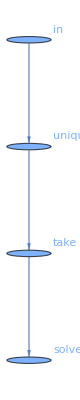

```mathematica
system // First // FFGraphDraw
```

We can now use FiniteFlow to reconstruct the output of the polynomial reduction with ReconstructPolynomialRemainder

```mathematica
results=ReconstructPolynomialRemainder[system]
```

Generated 18 sample points

Approximate time per evaluation (single core): 7e-06 sec.

{(1/2+(9 a)/2+3 a^2+(49 a^3)/16+a^3 b^2)/a^3+((-3-(117 a)/4-(171 a^2)/8-(7 a^3)/16) y)/a^3+((5/2+36 a+36 a^2+(41 a^3)/16) y^2)/a^3+((-3-(153 a)/4-(315 a^2)/8-(97 a^3)/16) y^3)/a^3+((1/2+(33 a)/2+(27 a^2)/2+(55 a^3)/16) y^4)/a^3+((-9/4-(9 a)/8-(9 a^2)/16) y^5)/a^2,7/2+s-(3 y)/2+y^2/2,9/4-(3 a)/16+(-3+(31 a)/16+a^2/32) y+(9/2-(75 a)/16-(3 a^2)/16) y^2+(-3/4+(95 a)/16+(11 a^2)/32) y^3+(-(45 a)/16-(3 a^2)/16) y^4+((7 a)/16+a^2/32) y^5}

We can check this result against Mathematica's built in functions GroebnerBasis and PolynomialReduce

```mathematica
gb = GroebnerBasis[ideal,variables,CoefficientDomain->RationalFunctions];
ansGB = PolynomialReduce[targets,gb,variables] // Map[Last] // Factor;
ansGB - results // Factor // ContainsOnly[{0}]
```

True

Note how we never needed an explicit Groebner Basis in the computation using SPQR. Only the output of the polynomial division is reconstructed. This is different to Mathematica, where if we don't build a Groebner Basis, the result of the polynomial reduction will not be well defined

```mathematica
ansNoGB = PolynomialReduce[targets,ideal,variables] // Map[Last] // Factor
ansNoGB - results // Factor // ContainsOnly[{0}]
```

{1/(4 a^3)(108-9 a+12 a^3+4 a^3 b^2+72 x+54 a x-120 x^2-36 a x^2-48 x^3-24 a x^3+32 x^4+16 a x^4+54 a y+2 a^3 y-90 a y^2+18 a^2 y^2-6 a^3 y^2+27 a y^3-54 a^2 y^3+2 a^3 y^3+18 a^2 y^4),1/2 (7+2 s-3 y+y^2),x^3}

False

### BuildPolynomialSystem in more detail

Let us examine the output of BuildPolynomialSystem in more detail

```mathematica
system
```

{SPQRGraph$484202,{a,b,s},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

system[[1]] is simply the name of the graph that has been built. system[[2]] is the list of parameters that is eventually reconstructed by FiniteFlow. In system[[3]], DepVars represents the list of the three target polynomials we are reducing.

IndepVars is the most important output, and represents the irreducible monomials that were found by the linear system during row reduction. These are completely analogous to the "master integrals" in an IBP reduction for Feynman integrals. They are indexed by the notation j[a,b] = x^a y^b

Specifically we have

```mathematica
"IndepVars" // ReplaceAll[system[[3]]]//ReplaceAll[j[x__]:>Times@@(variables^{x})]
```

{y^5,y^4,y^3,y^2,y,1}

How do we know if the monomials have been found are correct? We can verify using the command FindIrreducibleMonomials

```mathematica
irreducibleMonomials=FindIrreducibleMonomials[ideal,variables]
```

{y^5,y^4,y^3,y^2,y,1}

These can be passed as an option to BuildPolynomialSystem, which will automatically check if the irreducible monomials found by row reduction agree

If the output is as before, then the check has been passed

```mathematica
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials]
```

{SPQRGraph$484252,{a,b,s},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

If we however consider a system with too small of a seed, then in exact analogy to IBPs, the system will not reduce fully

```mathematica
maxWeight = 7;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials]
```

Irreducible monomials do not match. Try increasing the system size

Found 7 monomials: {x^5 y^7,y^5,y^4,y^3,y^2,y,1}

$Failed[7]

BuildPolynomialSystem also accepts a min and max weight input, which will automatically increase the seed until either max is reached or the system closes

```mathematica
system =BuildPolynomialSystem[targets,ideal,variables,{1,10},"IrreducibleMonomials"->irreducibleMonomials]
```

system closed at weight: 8

{SPQRGraph$484552,{a,b,s},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

Whenever possible, it is always recommended to precompute the irreducible monomials and to pass them as an option to BuildPolynomialSystem, in order to always insure a correct reduction when reconstruction is performed

### Changing Monomial Ordering

By default, Lexicographic order is used for computing divisions. This can be changed by passing the option "MonomialOrder". It is also possible to ask for verbose output during the construction of the system using "PrintDebugInfo", which accepts the values {0,1,2}.

Define an ideal and a target polynomials to reduce

```mathematica
variables = {x,y};
targets = {a*x^5*y^5*y^2+3+x*y^2+b^2,x*y+s+3,x^3};
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

```mathematica
irreducibleMonomials=FindIrreducibleMonomials[ideal,variables,"MonomialOrder"->DegreeReverseLexicographic]
```

{y^3,x^2,y^2,x,y,1}

Build the polynomial system and reconstruct the remainder

```mathematica
maxWeight = 8;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials,"MonomialOrder"->DegreeReverseLexicographic,"PrintDebugInfo"->2]
```

creating system seeds...done: 0.000175s

generating and sorting monomials...done: 0.000874s

preparing to generate system of size 93 x 86...done: 0.000457s

generating system...done: 0.000677s

building FiniteFlow Graph...done: 0.000336s

loading system data into FiniteFlow Graph...done: 0.001055s

learning irreducible monomials...done: 0.000162s

final number of equations needed: 22

{SPQRGraph$484593,{a,b,s},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,3],j[2,0],j[0,2],j[1,0],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

```mathematica
results=ReconstructPolynomialRemainder[system, "DeleteGraph" -> False]
```

Generated 21 sample points

Approximate time per evaluation (single core): 6e-06 sec.

{(-6-(45 a)/2-(291 a^2)/4-(9 a^3)/8+3 a^4+a^4 b^2)/a^4+((-9-(9 a)/2-(9 a^2)/4) x)/a^3+((4+24 a+54 a^2+a^3/2) x^2)/a^4+((-18-18 a+(63 a^2)/4+a^3/2) y)/a^3+((24+3 a-(153 a^2)/4-(3 a^3)/2) y^2)/a^3+((-9/2+(9 a)/4+(99 a^2)/8+a^3/2) y^3)/a^3,7/2+s-(3 y)/2+y^2/2,15/8-(3 a)/16+(7/4+a/8) x-(3 x^2)/2+(1/2+(5 a)/8) y+(-3/4-(3 a)/8) y^2+(1/8+a/16) y^3}

Check against built in functions

```mathematica
gb = GroebnerBasis[ideal,variables,CoefficientDomain->RationalFunctions,MonomialOrder->DegreeReverseLexicographic];
ansGB = PolynomialReduce[targets,gb,variables,MonomialOrder->DegreeReverseLexicographic] // Map[Last] // Factor;
ansGB - results // Factor // ContainsOnly[{0}]
```

True

For an exhaustive list of options, see the documentation function page BuildPolynomialSystem

## Examples from Paper

Here we provide the inputs and outputs of the SPQR code used in section 4 of the accompanying SPQR paper

### Resultant Computation

Computing the resultant

```mathematica
ideal={-1+a+x^2 y^2+y^3+z,-2+a x+c y+c x y^2+z^2,a+b+b x y^2+x^2 y^2,1-c+d x z+x y z};
variables=SortVariables[ideal,{x,y,z,d}]
```

{d,z,x,y}

```mathematica
irreds=FindIrreducibleMonomials[ideal,variables,"MonomialOrder"->DegreeReverseLexicographic]
cmats=BuildCompanionMatrices[ideal,variables,{1,10},irreds,"MonomialOrder"->DegreeReverseLexicographic]
```

{d^2,z^2,d x,x z,x^2,d y,y z,x y,y^2,d,z,x,y,1}

system closed at weight: 7

{SPQRGraph$486396,{a,b,c},{j[2,0,0,0],j[0,2,0,0],j[1,0,1,0],j[0,1,1,0],j[0,0,2,0],j[1,0,0,1],j[0,1,0,1],j[0,0,1,1],j[0,0,0,2],j[1,0,0,0],j[0,1,0,0],j[0,0,1,0],j[0,0,0,1],j[0,0,0,0]},{SPQR`Private`m[d$206],SPQR`Private`m[z$207],SPQR`Private`m[x$208],SPQR`Private`m[y$209]},{d,z,x,y}}

```mathematica
chard=BuildCharacteristicPolynomials[cmats,{1}];
res=ReconstructCharacteristicPolynomials[chard]//First;
```

Generated 6769 sample points

Approximate time per evaluation (single core): 0.000389 sec.

```mathematica
resultantSPQR=Power[d,Range[(irreds//Length)+1]-1].res//Factor//Numerator;
resultantSPQR
```

Checking against numerical slices

```mathematica
(*check for a*)
ksub={b,c,d}->RandomInteger[10^10,3]//Thread;
expr1=resultantSPQR//ReplaceAll[ksub];
expr2=GroebnerBasis[ideal//ReplaceAll[ksub],Complement[{a,b,c,d},ksub[[;;,1]]],{x,y,z},CoefficientDomain->RationalFunctions]//First;
expr1/expr2//Factor//Variables
(*check for b*)
ksub={a,c,d}->RandomInteger[10^10,3]//Thread;
expr1=resultantSPQR//ReplaceAll[ksub];
expr2=GroebnerBasis[ideal//ReplaceAll[ksub],Complement[{a,b,c,d},ksub[[;;,1]]],{x,y,z},CoefficientDomain->RationalFunctions]//First;
expr1/expr2//Factor//Variables
(*check for c*)
ksub={a,b,d}->RandomInteger[10^10,3]//Thread;
expr1=resultantSPQR//ReplaceAll[ksub];
expr2=GroebnerBasis[ideal//ReplaceAll[ksub],Complement[{a,b,c,d},ksub[[;;,1]]],{x,y,z},CoefficientDomain->RationalFunctions]//First;
expr1/expr2//Factor//Variables
```

{}

{}

{}

### Landau Computation

Setting up the problem

```mathematica
f={m2 x1^2 x2 x3+m2 x1 x2^2 x3+m2 x1 x2 x3^2+m2 x1^2 x2 x4+m2 x1 x2^2 x4+m2 x1^2 x3 x4+4 m2 x1 x2 x3 x4-t x1 x2 x3 x4+m2 x2^2 x3 x4+m2 x1 x3^2 x4+m2 x2 x3^2 x4+m2 x1 x2 x4^2+m2 x1 x3 x4^2+m2 x2 x3 x4^2+m2 x1^2 x2 x5+m2 x1 x2^2 x5+m2 x1^2 x3 x5+3 m2 x1 x2 x3 x5+m2 x1 x3^2 x5+3 m2 x1 x2 x4 x5+m2 x2^2 x4 x5+3 m2 x1 x3 x4 x5+3 m2 x2 x3 x4 x5+m2 x3^2 x4 x5+m2 x2 x4^2 x5+m2 x3 x4^2 x5+m2 x1 x2 x5^2+m2 x1 x3 x5^2+m2 x2 x4 x5^2+m2 x3 x4 x5^2+m2 x1^2 x3 x6+3 m2 x1 x2 x3 x6+m2 x2^2 x3 x6+m2 x1 x3^2 x6+m2 x2 x3^2 x6+m2 x1^2 x4 x6+3 m2 x1 x2 x4 x6+m2 x2^2 x4 x6+3 m2 x1 x3 x4 x6+3 m2 x2 x3 x4 x6+m2 x1 x4^2 x6+m2 x2 x4^2 x6+m2 x1^2 x5 x6+3 m2 x1 x2 x5 x6+m2 x2^2 x5 x6+4 m2 x1 x3 x5 x6-s x1 x3 x5 x6+3 m2 x2 x3 x5 x6+m2 x3^2 x5 x6+3 m2 x1 x4 x5 x6+4 m2 x2 x4 x5 x6+s x2 x4 x5 x6+t x2 x4 x5 x6+3 m2 x3 x4 x5 x6+m2 x4^2 x5 x6+m2 x1 x5^2 x6+m2 x2 x5^2 x6+m2 x3 x5^2 x6+m2 x4 x5^2 x6+m2 x1 x3 x6^2+m2 x2 x3 x6^2+m2 x1 x4 x6^2+m2 x2 x4 x6^2+m2 x1 x5 x6^2+m2 x2 x5 x6^2+m2 x3 x5 x6^2+m2 x4 x5 x6^2}//First;
(*Landau singularities are homogenous*)
ksub={t->1};
ideal=Join[{f},D[f,{{x1,x2,x3,x4,x5,x6}}],{1-x0*x1*x2*x3*x4*x5*x6}]/. ksub;
vars={m2,x0,x1,x2,x3,x4,x5,x6};
```

Verifying the ideal is not zero dimensional (this may take a few seconds)

```mathematica
FindIrreducibleMonomials[ideal,vars ,"MonomialOrder"->DegreeReverseLexicographic]
```

∞

Intersecting the ideal with a hyperplane and verifying it is zero dimensional

```mathematica
ideal0dim=ideal//ReplaceAll[x6->RandomInteger[{1,10^15}]];
vars0dim=vars[[1;;-2]];
irreds=FindIrreducibleMonomials[ideal0dim,vars0dim,"MonomialOrder"->DegreeReverseLexicographic]
irreds//Length
```

{x2 x4^2,x3 x4^2,x4^3,x3 x4 x5,x4^2 x5,m2 x5^2,x0 x5^2,x1 x5^2,x2 x5^2,x3 x5^2,x4 x5^2,x5^3,m2^2,m2 x0,x0^2,m2 x1,x0 x1,x1^2,m2 x2,x0 x2,x1 x2,x2^2,m2 x3,x0 x3,x1 x3,x2 x3,x3^2,m2 x4,x0 x4,x1 x4,x2 x4,x3 x4,x4^2,m2 x5,x0 x5,x1 x5,x2 x5,x3 x5,x4 x5,x5^2,m2,x0,x1,x2,x3,x4,x5,1}

48

Building the companion matrices (this may take some time)

```mathematica
cmats=BuildCompanionMatrices[ideal0dim,vars0dim,{11,15},irreds,"MonomialOrder"->DegreeReverseLexicographic,"PrintDebugInfo"->2];//AbsoluteTiming
```

creating system seeds...done: 0.061402s

generating and sorting monomials...done: 9.79292s

preparing to generate system of size 254928 x 215513...done: 4.48238s

generating system...done: 21.8006s

building FiniteFlow Graph...done: 0.001102s

loading system data into FiniteFlow Graph...done: 15.1502s

learning irreducible monomials...done: 221.253s

final number of equations needed: 57874

system closed at weight: 11

{281.449,Null}

Building and reconstructing the Eliminated system (this may take some time)

```mathematica
elimMons=FindEliminationMonomials[ideal0dim,{x0,x1,x2,x3,x4,x5},{m2}]
elimSyst=BuildEliminationSystems[cmats,elimMons];//AbsoluteTiming
elim=ReconstructEliminationSystems[elimSyst];//AbsoluteTiming
```

{{m2^27,m2^26,m2^25,m2^24,m2^23,m2^22,m2^21,m2^20,m2^19,m2^18,m2^17,m2^16,m2^15,m2^14,m2^13,m2^12,m2^11,m2^10,m2^9,m2^8,m2^7,m2^6,m2^5,m2^4,m2^3,m2^2,m2,1}}

{54.8108,Null}

Generated 27 sample points

Approximate time per evaluation (single core): 19.0884 sec.

Generated 27 sample points

Approximate time per evaluation (single core): 19.0803 sec.

{1073.83,Null}

Extracting the singularities

```mathematica
elimNumerator=elim//First//Together//Numerator;
landauinhomog=elimNumerator//FactorList//Flatten//DeleteCases[x_/;IntegerQ[x]];
landau=landauinhomog//Map[ResourceFunction["PolynomialHomogenize"][#,{s,m2},t]&]//Sort;
landau//TableForm
```

27 m2^3+4 s^2 t+4 s t^2
27 m2^4 s^2+108 m2^4 s t+162 m2^3 s^2 t+54 m2^2 s^3 t+4 m2 s^4 t+108 m2^4 t^2+162 m2^3 s t^2+45 m2^2 s^2 t^2-6 m2 s^3 t^2-s^4 t^2-18 m2^2 s t^3-20 m2 s^2 t^3-2 s^3 t^3-9 m2^2 t^4-10 m2 s t^4-s^2 t^4
108 m2^4 s^2-9 m2^2 s^4+108 m2^4 s t+162 m2^3 s^2 t-18 m2^2 s^3 t-10 m2 s^4 t+27 m2^4 t^2+162 m2^3 s t^2+45 m2^2 s^2 t^2-20 m2 s^3 t^2-s^4 t^2+54 m2^2 s t^3-6 m2 s^2 t^3-2 s^3 t^3+4 m2 s t^4-s^2 t^4
27 m2^4 s^2-54 m2^4 s t+162 m2^3 s^2 t-54 m2^2 s^3 t+4 m2 s^4 t+27 m2^4 t^2+162 m2^3 s t^2-117 m2^2 s^2 t^2+22 m2 s^3 t^2-s^4 t^2-54 m2^2 s t^3+22 m2 s^2 t^3-2 s^3 t^3+4 m2 s t^4-s^2 t^4
65536 m2^12+270336 m2^10 s^2+33024 m2^8 s^4+1024 m2^6 s^6+270336 m2^10 s t-458752 m2^9 s^2 t+66048 m2^8 s^3 t-1276416 m2^7 s^4 t+3072 m2^6 s^5 t-137472 m2^5 s^6 t-4096 m2^3 s^8 t+270336 m2^10 t^2-458752 m2^9 s t^2+99072 m2^8 s^2 t^2-2552832 m2^7 s^3 t^2-3427584 m2^6 s^4 t^2-412416 m2^5 s^5 t^2+149472 m2^4 s^6 t^2-16384 m2^3 s^7 t^2+768 m2^2 s^8 t^2+66048 m2^8 s t^3-2552832 m2^7 s^2 t^3-6860288 m2^6 s^3 t^3-687360 m2^5 s^4 t^3+448416 m2^4 s^5 t^3-49888 m2^3 s^6 t^3+3072 m2^2 s^7 t^3-48 m2 s^8 t^3+33024 m2^8 t^4-1276416 m2^7 s t^4-3427584 m2^6 s^2 t^4-687360 m2^5 s^3 t^4+597888 m2^4 s^4 t^4-92320 m2^3 s^5 t^4+6144 m2^2 s^6 t^4-192 m2 s^7 t^4+s^8 t^4+3072 m2^6 s t^5-412416 m2^5 s^2 t^5+448416 m2^4 s^3 t^5-92320 m2^3 s^4 t^5+7680 m2^2 s^5 t^5-336 m2 s^6 t^5+4 s^7 t^5+1024 m2^6 t^6-137472 m2^5 s t^6+149472 m2^4 s^2 t^6-49888 m2^3 s^3 t^6+6144 m2^2 s^4 t^6-336 m2 s^5 t^6+6 s^6 t^6-16384 m2^3 s^2 t^7+3072 m2^2 s^3 t^7-192 m2 s^4 t^7+4 s^5 t^7-4096 m2^3 s t^8+768 m2^2 s^2 t^8-48 m2 s^3 t^8+s^4 t^8

Related Guides

SPQR

Related Tech Notes

## Metadata

### Categorization

Tech Note

SPQR

SPQR`

SPQR/tutorial/IntroductiontoSPQR

### Keywords